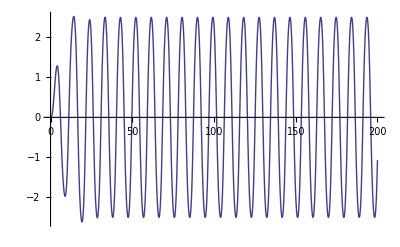

```mathematica
sol[γ_,A_,Ω_,p_]:=NDSolve[{θ''[t]+γ θ'[t]+Sin[θ[t]]==A Sin[Ω t],θ[0]==0,θ'[0]==0},θ,{t,0,2000},MaxSteps->Infinity,WorkingPrecision->p];
Plot[Evaluate[θ[t]/.sol[5/10,9000/10000,2/3,25]],{t,0,200},PlotRange->All]
```

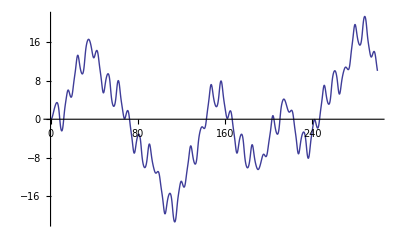

```mathematica
Plot[Evaluate[θ[t]/.sol[5/10,149/100,2/3,25]],{t,0,300},PlotRange->All]
```

```mathematica
θ[50]/.sol[5/10,149/100,2/3,25]
```

```mathematica
{7.0343718569602239903278890564488469946709922366256123064653`23.442588313559135}
```

```mathematica
θ[300]/.sol[5/10,149/100,2/3,25]
```

{10.070409600640683503886}

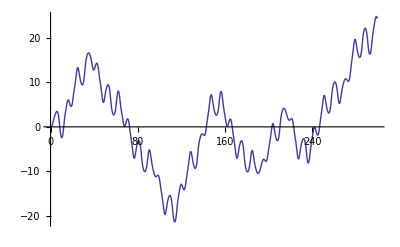

```mathematica
Plot[Evaluate[θ[t]/.sol[5/10,149/100,2/3,45]],{t,0,300},PlotRange->All]
```

```mathematica
θ[50]/.sol[5/10,149/100,2/3,45]
```

```mathematica
{7.03437185697296293699554075321720210148675666168697200302058386548571762070079`43.47739124540075}
```

```mathematica
θ[300]/.sol[5/10,149/100,2/3,45]
```

{24.37656119448806115181331314805605081992438}

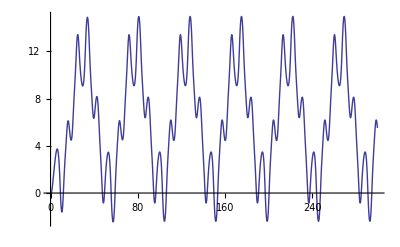

```mathematica
Plot[Evaluate[θ[t]/.sol[5/10,151/100,2/3,25]],{t,0,300},PlotRange->All]
```

```mathematica
θ[80]/.sol[5/10,151/100,2/3,25]
```

```mathematica
{14.2269063397920085435689966232254221472192427751567556693651`23.542949228958754}
```

```mathematica
θ[80]/.sol[5/10,151/100,2/3,35]
```

```mathematica
{14.2269063396878882774375624406467407021186165759097454285662`33.61931512493364}
```

```mathematica
θ[80]/.sol[5/10,151/100,2/3,45]
```

```mathematica
{14.22690633968788624135154109722673717336987237178058776898325825032661105092516`43.58485976478486}
```

```mathematica
θ[80]/.sol[5/10,151/100,2/3,50]
```

```mathematica
{14.22690633968788623200748744024069205405283986579824586324730959192075174841601`48.554118903657944}
```

```mathematica
value80[p_]:=θ[80]/.sol[5/10,151/100,2/3,p]
```

```mathematica
(14.22690633968788623200748744024069-14.22690633979200854356899662322542)/14.22690633968788623200748744024069
```

-7.31868960654122411089×10^-12

```mathematica
hh=Table[-Log[Abs[(14.22690633968788623200748744024069-value80[p])/14.22690633968788623200748744024069]],{p,10,45}]
```

{{9.2077},{10.4131},{12.2015},{12.73117},{14.56703},{15.941881},{16.542982},{17.0075454},{19.0629731},{20.00139798},{19.075785659},{21.304735739},{23.1737624794},{22.8701536746},{25.23284615213},{25.64058981948},{28.163219891502},{29.095695181683},{28.1563354804358},{30.0151489463431},{30.36596664135478},{35.1883976327815},{36.41047980105655},{34.7115619334876742},{35.9767299697927975},{36.4783033062716123},{38.511668425635263},{38.1692648414539684},{38.729828604333823},{41.04032156971019},{38.736084141960386},{41.38914823648457},{43.5204902894876},{39.715432034995401},{45.75322868135},{41.86692648979163}}

```mathematica
hh[[1,1]]
```

9.2077

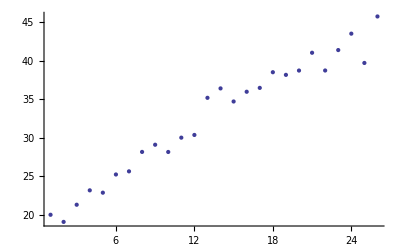

```mathematica
ListPlot[Table[{k-9,hh[[k,1]]},{k,10,35}]]
```

```mathematica
θ[220]/.sol[5/10,151/100,2/3,25]
```

```mathematica
{11.1510932470505572057788129238165597757248104586620850998361`22.860975727539554}
```

```mathematica
θ[220]/.sol[5/10,151/100,2/3,45]
```

```mathematica
{11.15109324698078602650504068091828390338991877533995294619261326432830406796482`43.179424519502206}
```